```mathematica
<<Radia`
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Chopped Cylinder

```mathematica
dout=40; (* outer diameter *)
din=5; (* inner bore *)
dz=8; (* stage thickness *)
Nwedge=12; (* number of wedges *)
Mr=1.44; (* remanent magnetization *)
(*KK =2; (* type of Halbach array *)*)
dθ=360/Nwedge; (* angular extent of each wedge *)


(* some plot options *)
c2 = {0.5,0,0.5};
c6={0,0.5,0};
thcn = 0.001;

makeKstage[KK_,zoff_,ϕrot_,cnt_]:=Module[{},stage={};
(*KK=6;
zoff=0;*)
For[w=1,w≤Nwedge,w++,
θu=-(w-1)*dθ*Pi/180-ϕrot;
θl=w*dθ*Pi/180+ϕrot;
ϕ = 2Pi/Nwedge(w-1/2);
Mvec=Mr{Cos[KK ϕ+ϕrot],Sin[KK ϕ+ϕrot],0};
cyl=radObjCylMag[{0,0,zoff},dout/2,dz,120,"z",Mvec];
cyl=radObjCutMag[cyl,{0,0,0},{0,Sin[θl],-Cos[θl]}][[2]];
cyl=radObjCutMag[cyl,{0,0,0},{0,Sin[θu],Cos[θu]}][[2]];
cyl=radObjCutMag[cyl,din/2*{0,Cos[θl-dθ Pi/360],Sin[θl-dθ Pi/360]},{0, Cos[θl-dθ Pi/360],Sin[θl-dθ Pi/360]}][[2]];
radObjDrwAtr[cyl,If[KK==2,{1,1,0},{1,0,1}],3*thcn];
AppendTo[stage,cyl];
Clear[cyl];
];
radObjAddToCnt[cnt,stage];
];
```

```mathematica
m=6;
1.44{Cos[2 2Pi/12(m-1/2)],Sin[2 2Pi/12(m-1/2)],0}
```

{1.24708,-0.72,0.}

```mathematica
?Rad*
```

```mathematica
radUtiDelAll[];
Grp=radObjCnt[{}];
nstage=8;
angles={Pi/2,0,Pi/2,Pi,Pi/2,0,Pi/2,Pi};
Do[makeKstage[If[EvenQ[i],2,6],(i-1)*10,angles[[i]],Grp],{i,1,nstage}]

Grp
```

1

```mathematica
(* Special options for the Plot[] *)
RadPlot3DOptions[];
(* save the geometry in "dr" *)
dr = radObjDrw[Grp];
(* draw the geometry *)
Show[Graphics3D[dr],FrameLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
res=RadSolve[stage,0.001,200];
```

```mathematica
xlim=2.5;
ylim=2.5;
zmin=0;
zmax=110;

BnormXcut=Table[{x,Sqrt[radFld[Grp,"bx",{x,0,0}]^2+radFld[Grp,"by",{x,0,0}]^2+radFld[Grp,"bz",{x,0,0}]^2]},{x,-xlim,xlim,1}];
BnormYcut=Table[{y,Sqrt[radFld[Grp,"bx",{0,y,0}]^2+radFld[Grp,"by",{0,y,0}]^2+radFld[Grp,"bz",{0,y,0}]^2]},{y,-ylim,ylim,1}];
BnormZcut=Table[{z,Sqrt[radFld[Grp,"bx",{0,1,z}]^2+radFld[Grp,"by",{0,1,z}]^2+radFld[Grp,"bz",{0,1,z}]^2]},{z,zmin,zmax,.1}];
dnormBdz=Differences[BnormZcut[[;;,2]]]/.{x_,y_}->y/x;
dBtab=Table[{BnormZcut[[i,1]],60dnormBdz[[i]]},{i,1,Length[BnormZcut]-1}];
```

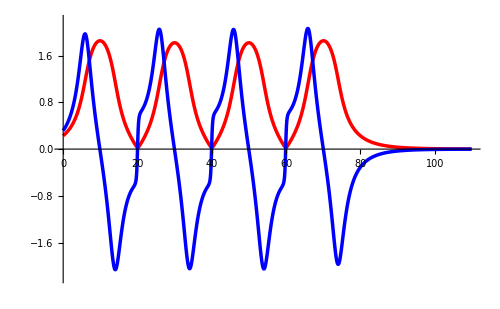

```mathematica
Bplot=ListPlot[BnormZcut,Joined->True,PlotStyle->{Red,Thickness[0.005]},PlotRange->{-2.2,2.2}];
dBplot=ListPlot[dBtab,Joined->True,PlotStyle->{Blue,Thickness[0.005]}];
Show[Bplot,dBplot,ImageSize->500]
```

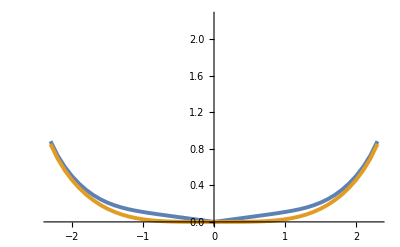

```mathematica
zoffset=40;
xlim=2.3;
BnormXcut=Table[{x,Sqrt[radFld[Grp,"bx",{x,0,zoffset}]^2+radFld[Grp,"by",{x,0,zoffset}]^2+radFld[Grp,"bz",{x,0,zoffset}]^2]},{x,-xlim,xlim,0.1}];
BnormYcut=Table[{x,Sqrt[radFld[Grp,"bx",{0,x,zoffset}]^2+radFld[Grp,"by",{0,x,zoffset}]^2+radFld[Grp,"bz",{0,x,zoffset}]^2]},{x,-xlim,xlim,0.1}];
ListPlot[{BnormXcut,BnormYcut},Joined->True,PlotStyle->{Thickness[0.007]},PlotRange->{0,2.25}]
```

```mathematica
contour2D=Table[{z,x,Sqrt[radFld[Grp,"bx",{x,0,z}]^2+radFld[Grp,"by",{x,0,z}]^2+radFld[Grp,"bz",{x,0,z}]^2]},{z,20,70,0.25},{x,-2.5,2.5,0.5}];
contour2D=ArrayReshape[contour2D,{Dimensions[contour2D][[1]]*Dimensions[contour2D][[2]],3}];
(*Bvecplot=Table[{{z,x},{radFld[Grp,"bz",{x,0,z}],radFld[Grp,"bx",{x,0,z}]}},{z,55,65,1},{x,-2,2,1}];*)
```

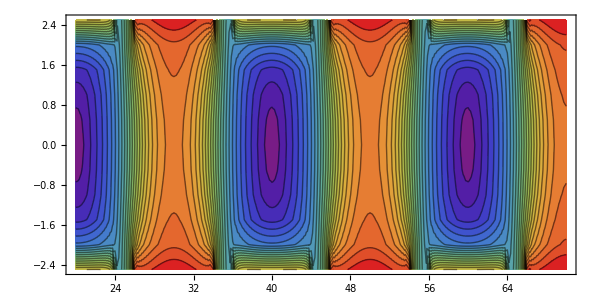

```mathematica
Bcont=ListContourPlot[contour2D,Contours->25,AspectRatio->0.5,ImageSize->600,ColorFunction->"Rainbow",PlotLegends->Automatic];
(*Bvec=ListVectorPlot[Bvecplot,AspectRatio->1,ImageSize->300,VectorStyle->{White}];
Show[Bcont,Bvec]*)
Show[Bcont]
```

```mathematica
zoff=40;
contourKstage=Table[{Sqrt[radFld[Grp,"bx",{x,y,zoff}]^2+radFld[Grp,"by",{x,y,zoff}]^2+radFld[Grp,"bz",{x,y,zoff}]^2]},{x,-2.5,2.5,0.1},{y,-2.5,2.5,0.1}];
```

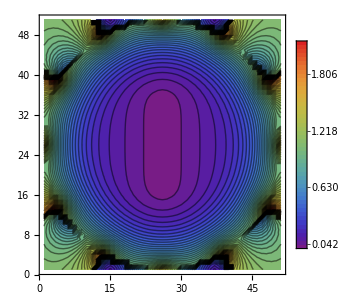

```mathematica
ListContourPlot[Transpose[contourKstage[[;;,;;,1]]],Contours->50,AspectRatio->1,ImageSize->300,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
?ListContourPlot
```

ListContourPlot[array] generates a contour plot from an array of height values. 
ListContourPlot[{{x_1,y_1,f_1},{x_2,y_2,f_2},…}] generates a contour plot from values defined at specified points.

```mathematica
?rad*
```

```mathematica
radUtiDelAll[]
```

0

## Radia Materials

```mathematica
<<Radia`
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
createWedge[npts_,din_,dout_,θmin1_,θmax1_]:=Module[{},
poly={};
(* initialize constants *)
θmin=θmin1*Pi/180 ;
θmax=θmax1*Pi/180;
dθ=(θmax-θmin)/npts;
poly={};
(* make innner cirlce *)
For[n=0,n≤npts,n++,
θ=θmin+n*dθ;
AppendTo[poly,din/2*{Cos[θ],Sin[θ]}]]
(* make first connecting line *)
AppendTo[poly,dout/2*{Cos[θ],Sin[θ]}];
(* make outer circle *)
For[n=0,n≤npts,n++,
θ=θmax-(θmax-θmin)/npts*n;
AppendTo[poly,dout/2*{Cos[θ],Sin[θ]}]];
(* close the polygon *)
θ=θmin;
AppendTo[poly,din/2*{Cos[θ],Sin[θ]}]
];
```

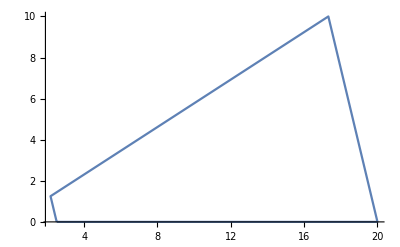

```mathematica
createWedge[1,5,40,360,390];
ListPlot[poly,Joined->True,PlotRange->All]
```

```mathematica
radObjThckPgn[0,8,poly[[1;;-2]],"x"]
```

26

```mathematica
?radObjThckPgn
```

radObjThckPgn[x,lx,{{y1,z1},{y2,z2},...},a:"x",{mx,my,mz}:{0,0,0}] creates an extruded polygon block; x is the position of the block's center of gravity in the extrusion direction, lx is the thickness, {{y1,z1},{y2,z2},...} is a list of points describing the polygon in 2D; the extrusion direction is defined by the character a (which can be "x", "y" or "z"), {mx,my,mz} is the block magnetization.

```mathematica
?RadMatNdFeB
```

RadMatNdFeB[Mr:1.2] creates a NdFeB magnetic material with remanent magnetization Mr. The direction of the remanent magnetization vector is defined by the initial magnetization vector in the object to which the material is later applied.

```mathematica
Nwedge=12;
din=6;
dout=40;
(*zoffset=0;*)
dz=8;
Mr=1;
magmat=RadMatNdFeB[];
makeKstage[KK_,zoff_,ϕrot_,cnt_]:=Module[{},
(* make wedge outlines *)
allpolys={};
For[w=1,w≤Nwedge,w++,
createWedge[1,din,dout,360/Nwedge*(w-1),360/Nwedge*w];
AppendTo[allpolys,poly[[1;;-2]]];
ϕ=2Pi/Nwedge(w-1/2);
Mvec=Mr{Cos[KK ϕ],Sin[KK ϕ],0};
rot={{Cos[ϕrot],Sin[ϕrot],0},{-Sin[ϕrot],Cos[ϕrot],0},{0,0,1}};
Mvec=rot.Mvec;
obj=radObjThckPgn[zoff,dz,allpolys[[w]],"z",Mvec];
(*radMatApl[obj,magmat];*)
radObjAddToCnt[cnt,{obj}]
];
];
```

```mathematica
obj
```

obj

```mathematica
radUtiDelAll[];
stage=radObjCnt[{}];
nstage=16;
(*Do[makeKstage[If[EvenQ[i],6,2],i*10,If[EvenQ[i],Pi/2,Mod[i,2]*Pi],stage],{i,0,nstage-1}]*)
(*makeKstage[6,0,Pi/2,stage]*)
makeKstage[6,0,Pi/2,stage]
makeKstage[2,10,0,stage]
makeKstage[6,20,Pi/2,stage]
makeKstage[2,30,Pi,stage]
makeKstage[6,40,Pi/2,stage]
makeKstage[2,50,0,stage]
makeKstage[6,60,Pi/2,stage]
makeKstage[2,70,Pi,stage]
makeKstage[6,80,Pi/2,stage]
makeKstage[2,90,0,stage]
makeKstage[6,100,Pi/2,stage]
makeKstage[2,110,Pi,stage]
makeKstage[6,120,Pi/2,stage]
```

```mathematica
Table[Mod[i,2]*Pi,{i,0,5}]
```

{0,π,0,π,0,π}

```mathematica
{0,π,0,π,0,π}
```

{0,π,0,π,0,π}

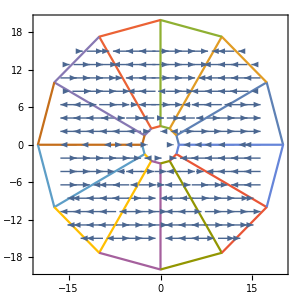

```mathematica
zoff=0;
Mplot=Table[{{x,y},{radFld[stage,"mx",{x,y,zoff}],radFld[stage,"my",{x,y,zoff}]}},{x,-15,15,1},{y,-15,15,1}];
p1=ListVectorPlot[Mplot,AspectRatio->1,ImageSize->300,ColorFunction->"Rainbow",PlotLegends->Automatic];
p2=ListPlot[allpolys,Joined->True];
Show[p1,p2,PlotRange->{{-20,20},{-20,20}}]
```

```mathematica
res=RadSolve[stage,0.00001,20000];
```

Radia::Error118: Failed to create Interaction Matrix.

Radia::Error000: Incorrect input: Function arguments.

```mathematica
(* Special options for the Plot[] *)
RadPlot3DOptions[];
(* save the geometry in "dr" *)
dr = radObjDrw[stage];
(* draw the geometry *)
Show[Graphics3D[dr],FrameLabel->{"X","Y","Z"}]
```

-Graphics3D-

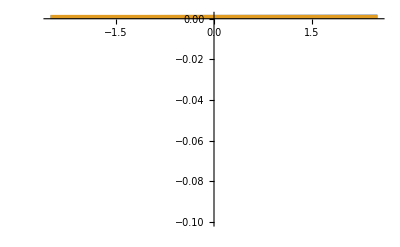

```mathematica
zoffset=50;
xlim=2.5;
BnormXcut=Table[{x,Sqrt[radFld[stage,"bx",{x,0,zoffset}]^2+radFld[stage,"by",{x,0,zoffset}]^2+radFld[stage,"bz",{x,0,zoffset}]^2]},{x,-xlim,xlim,0.1}];
BnormYcut=Table[{x,Sqrt[radFld[stage,"bx",{0,x,zoffset}]^2+radFld[stage,"by",{0,x,zoffset}]^2+radFld[stage,"bz",{0,x,zoffset}]^2]},{x,-xlim,xlim,0.1}];
ListPlot[{BnormXcut,BnormYcut},Joined->True,PlotStyle->{Thickness[0.007]},PlotRange->{-0.1,All}]
```

```mathematica
xoff=5;
yoff=-5;
zoff=0;
{radFld[stage,"mx",{xoff,yoff,zoff}],radFld[stage,"my",{xoff,yoff,zoff}],radFld[stage,"mz",{xoff,yoff,zoff}]}/Sqrt[1.44]
```

{0.833333,-5.99863×10^-30,1.79753×10^-32}

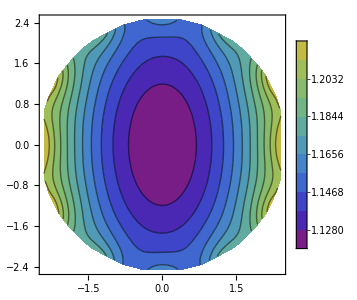

```mathematica
zoff=50;
contourKstage=Table[{x,y,
If[Abs[y]<Sqrt[2.5^2-x^2],Sqrt[radFld[stage,"hx",{x,y,zoff}]^2+radFld[stage,"hy",{x,y,zoff}]^2+radFld[stage,"hz",{x,y,zoff}]^2],Infinity]},{y,-2.5,2.5,0.05},{x,-2.5,2.5,0.1}];
contourKstage=ArrayReshape[contourKstage,{Dimensions[contourKstage][[1]]*Dimensions[contourKstage][[2]],3}];
ListContourPlot[contourKstage,Contours->10,AspectRatio->1,ImageSize->300,ColorFunction->ColorData[{"Rainbow",{0,1.5}}],PlotLegends->Automatic]
```

```mathematica
xlim=2.5;
ylim=2.5;
zmin=40;
zmax=80;

BnormXcut=Table[{x,Sqrt[radFld[stage,"bx",{x,0,0}]^2+radFld[stage,"by",{x,0,0}]^2+radFld[stage,"bz",{x,0,0}]^2]},{x,-xlim,xlim,1}];
BnormYcut=Table[{y,Sqrt[radFld[stage,"bx",{0,y,0}]^2+radFld[stage,"by",{0,y,0}]^2+radFld[stage,"bz",{0,y,0}]^2]},{y,-ylim,ylim,1}];
BnormZcut=Table[{z,Sqrt[radFld[stage,"bx",{0,0,z}]^2+radFld[stage,"by",{0,0,z}]^2+radFld[stage,"bz",{0,0,z}]^2]},{z,zmin,zmax,0.1}];
dnormBdz=Differences[BnormZcut[[;;,2]]]/.{x_,y_}->y/x;
dBtab=Table[{BnormZcut[[i,1]],60dnormBdz[[i]]},{i,1,Length[BnormZcut]-1}];
```

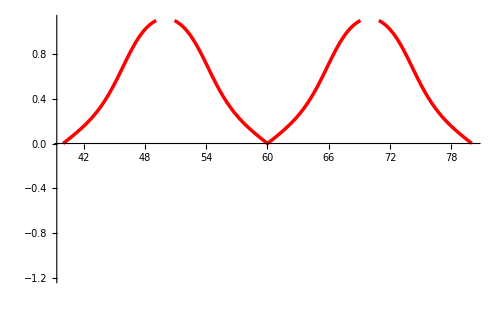

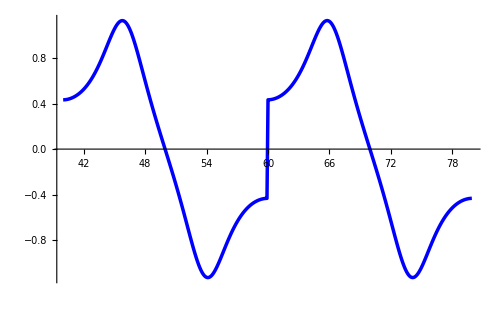

```mathematica
Bplot=ListPlot[BnormZcut,Joined->True,PlotStyle->{Red,Thickness[0.005]},PlotRange->{-1.2,1.1}]
dBplot=ListPlot[dBtab,Joined->True,PlotStyle->{Blue,Thickness[0.005]}]
```

```mathematica
contour2D=Table[{Sqrt[radFld[stage,"bx",{x,0,z}]^2+radFld[stage,"by",{x,0,z}]^2+radFld[stage,"bz",{x,0,z}]^2]},{z,20,60,0.5},{x,-2.5,2.5,0.05}];
```

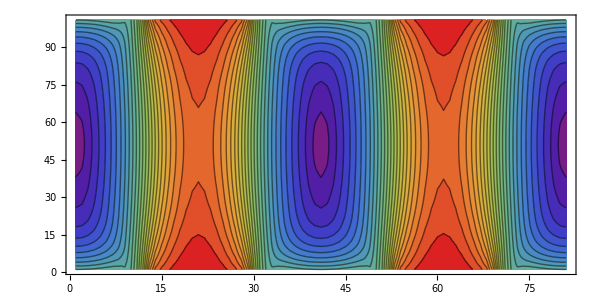

```mathematica
ListContourPlot[Transpose[contour2D[[;;,;;,1]]],Contours->25,AspectRatio->0.5,ImageSize->600,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
Bvec=Table[{radFld[stage,"bx",{x,y,z}],radFld[stage,"by",{x,y,z}],radFld[stage,"bz",{x,y,z}]},{x,-2.5,2.5,0.1},{y,-2.5,2.5,0.1},{z,20,60,0.5}];
```

```mathematica
Bnorm=Table[Sqrt[radFld[stage,"bx",{x,y,z}]^2+radFld[stage,"by",{x,y,z}]^2+radFld[stage,"bz",{x,y,z}]^2],{x,-2.5,2.5,0.1},{y,-2.5,2.5,0.1},{z,20,60,0.5}];
```

```mathematica
Bx=ListInterpolation[Bvec[[;;,;;,;;,1]],{{-2.5*^-3,2.5*^-3},{-2.5*^-3,2.5*^-3},{0,40*^-3}}];
By=ListInterpolation[Bvec[[;;,;;,;;,2]],{{-2.5*^-3,2.5*^-3},{-2.5*^-3,2.5*^-3},{0,40*^-3}}];
Bz=ListInterpolation[Bvec[[;;,;;,;;,3]],{{-2.5*^-3,2.5*^-3},{-2.5*^-3,2.5*^-3},{0,40*^-3}}];
normB=ListInterpolation[Sqrt[Bvec[[;;,;;,;;,1]]^2+Bvec[[;;,;;,;;,2]]^2+Bvec[[;;,;;,;;,3]]^2],{{-2.5*^-3,2.5*^-3},{-2.5*^-3,2.5*^-3},{0,40*^-3}}];
```

```mathematica
normB[0,-2.5mm,0]
```

0.395371

```mathematica
SetDirectory[NotebookDirectory[]];
Bx >> "Bx.m"
By >> "By.m"
Bz >> "Bz.m"
normB >> "normB.m"
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Ben/Google Drive/Doyle Group/Simulations/Zeeman Sisyphus

## Fitted Fields

```mathematica
SFSy[y_]:=-6267.y^2-0.106y+1.018;
SFSx[x_]:=(2.518*^4)x^2-0.05364x+1.021;
WFSy[y_]:=(1.081*^10)y^4+(1.635*^5)y^3-(1.133*^4)y^2-0.6312y+0.02394;
WFSx[x_]:=(7.657*^9)x^4-(1.166*^5)x^3+(3.603*^4)x^2+0.2786x+0.03799;
fz[z_]:=0.5275+0.4828*Cos[315.3*z+3.118];
```

```mathematica
mm=1.*^-3;
```

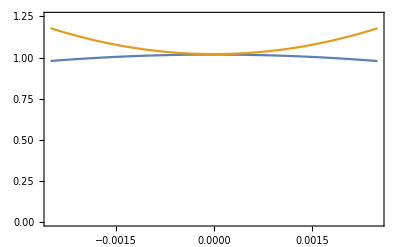

```mathematica
Plot[{SFSy[y],SFSx[y]},{y,-2.5mm,2.5mm},PlotRange->{0,1.25},Frame->True,Axes->False]
```

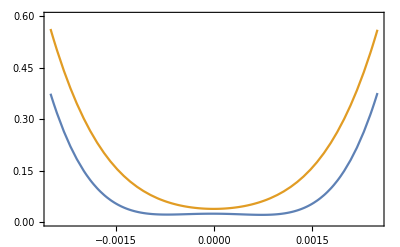

```mathematica
Plot[{WFSy[s],WFSx[s]},{s,-2.5mm,2.5mm},PlotRange->{0,0.6},Frame->True,Axes->False]
```

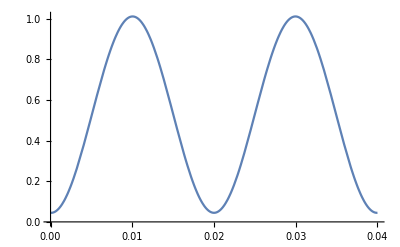

```mathematica
Plot[fz[z],{z,0mm,40mm}]
```

```mathematica
xcut[x_,z_]:=SFSx[x]Sin[315.3z/2]^2+WFSx[x]Cos[315.3z/2]^2
ycut[y_,z_]:=SFSy[y]Sin[315.3z/2]^2+WFSy[y]Cos[315.3z/2]^2
```

```mathematica
fullfield[x_,y_,z_]:=SFSx[x]SFSy[y]Sin[315.3z/2]^2+WFSx[x]WFSy[y]Cos[315.3z/2]^2
```

```mathematica
sfstab=Table[If[Abs[y]<Sqrt[(2.5mm)^2-x^2],fullfield[x,y,30mm],Infinity],{x,-2.5mm,2.5mm,0.025mm},{y,-2.5mm,2.5mm,0.025mm}];
wfstab=Table[If[Abs[y]<Sqrt[(2.5mm)^2-x^2],fullfield[x,y,20mm],Infinity],{x,-2.5mm,2.5mm,0.025mm},{y,-2.5mm,2.5mm,0.025mm}];
```

```mathematica
ListDensityPlot[Transpose@sfstab,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics-

```mathematica
epi=ListContourPlot[Transpose@wfstab,Contours->{{1.04,Thick}},ContourShading->None];
ListDensityPlot[Transpose@wfstab,ColorFunction->"Rainbow",Epilog->epi]
```

-Graphics-